# Textual Patterns in Tweets

## Jeffrey Starr - 2013 October 01

## Data Source

On October 1, using Twitter’s statuses/sample API, I sampled approximately 150 megabytes of tweets. The file contains 115,228 lines according to ‘wc’; since each tweet is delimited by two newlines, the raw contents should contain half the number of lines or 57,614 tweets.

```mathematica
rawtweets=ReadList["Data/tweets_20131001.json",String];
```

```mathematica
Length[rawtweets]
```

57614

For our analysis, we only want tweets in English, so we need to filter the list by the lang attribute equaling “en”. Additionally, we will convert the string representation into a set of rules by having Mathematica interpret the JSON object.

<< Grr, you can have multiple lang references in a tweet. Have to be more sophisticated than simply looking for “lang”:”en” >>

```mathematica
rawtweets[[45]]
```

{"created_at":"Tue Oct 01 21:52:14 +0000 2013","id":385160251995348993,"id_str":"385160251995348993","text":"@_CiaraTaylor_ OMG only just saw this! One of the best moments of school life, we couldn't breath.","source":"\u003ca href=\"http:\/\/twitter.com\/download\/iphone\" rel=\"nofollow\"\u003eTwitter for iPhone\u003c\/a\u003e","truncated":false,"in_reply_to_status_id":384950659675860992,"in_reply_to_status_id_str":"384950659675860992","in_reply_to_user_id":406566124,"in_reply_to_user_id_str":"406566124","in_reply_to_screen_name":"_CiaraTaylor_","user":{"id":901702921,"id_str":"901702921","name":"Jai We Love You. ","screen_name":"_JanoskiansILY","location":"liverpool, England","url":null,"description":"@Luke_brooks surprise followed me on 22.3.13 cause he secretly wants me. @James_yammouni followed 21.3.13 NOTAFUCKINGBOYBAND. 25.5.13 I saw them BESTNIGHTEVER","protected":false,"followers_count":2777,"friends_count":2497,"listed_count":0,"created_at":"Wed Oct 24 12:03:03 +0000 2012","favourites_count":611,"utc_offset":0,"time_zone":"Casablanca","geo_enabled":false,"verified":false,"statuses_count":6213,"lang":"en","contributors_enabled":false,"is_translator":false,"profile_background_color":"C0DEED","profile_background_image_url":"http:\/\/a0.twimg.com\/profile_background_images\/877598069\/a98280bbb8175d3ea51e6f76f1220a2e.jpeg","profile_background_image_url_https":"https:\/\/si0.twimg.com\/profile_background_images\/877598069\/a98280bbb8175d3ea51e6f76f1220a2e.jpeg","profile_background_tile":true,"profile_image_url":"http:\/\/a0.twimg.com\/profile_images\/378800000530304707\/0d1199ea2ee9c36092d0634d5718e3b2_normal.jpeg","profile_image_url_https":"https:\/\/si0.twimg.com\/profile_images\/378800000530304707\/0d1199ea2ee9c36092d0634d5718e3b2_normal.jpeg","profile_banner_url":"https:\/\/pbs.twimg.com\/profile_banners\/901702921\/1379100970","profile_link_color":"0084B4","profile_sidebar_border_color":"FFFFFF","profile_sidebar_fill_color":"DDEEF6","profile_text_color":"333333","profile_use_background_image":true,"default_profile":false,"default_profile_image":false,"following":null,"follow_request_sent":null,"notifications":null},"geo":null,"coordinates":null,"place":null,"contributors":null,"retweet_count":0,"favorite_count":0,"entities":{"hashtags":[],"symbols":[],"urls":[],"user_mentions":[{"screen_name":"_CiaraTaylor_","name":"Ciara Taylor","id":406566124,"id_str":"406566124","indices":[0,14]}]},"favorited":false,"retweeted":false,"filter_level":"medium","lang":"en"}

```mathematica
entweets=Cases[ImportString[#,"JSON"]&/@rawtweets,{__,"lang"->"en",___}];
```

```mathematica
Length[entweets]
```

20043

After filtering for language, we are left with 20,043 tweets, or a bit less than half the contents in the original dataset.

Finally, tweets come with a rich set of metadata that isn’t useful for our purposes. Our next step is to filter the tweets to just the 140 character maximum messages.

```mathematica
payload=(#/.{___,"text"->t_,___}->t)&/@entweets;
```

```mathematica
Length[payload]
```

20043

```mathematica
Min[StringLength[#]&/@payload]
```

5

```mathematica
Median[StringLength[#]&/@payload]
```

70

```mathematica
Max[StringLength[#]&/@payload]
```

374

Due to escaped characters (e.g. & encoded as &amp;), the length of tweets can be greater than the well-known 140 character limit.

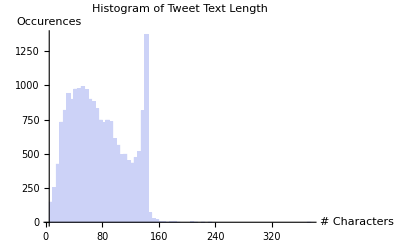

```mathematica
Histogram[StringLength[#]&/@payload,PlotLabel->"Histogram of Tweet Text Length",
AxesLabel->{"# Characters","Occurences"}
]
```

For a list of messages and a given order, return a table (list) containing n+1 tuples with the first n entries in the tuple representing characters and the final entry representing the frequency of those n characters found within texts.

```mathematica
NthOrderTally[texts_,n_]:=
Flatten[#]&/@
Tally[
Flatten[
Partition[Characters[#],n,1]&/@texts,
1]
]
```

```mathematica
n1table=NthOrderTally[payload,1];
```

```mathematica
Length[n1table]
```

787

```mathematica
n2table=NthOrderTally[payload,2];
```

```mathematica
Length[n2table]
```

8976

```mathematica
n2table[[1]]
```

{W,h,803}

```mathematica
n2table[[2]]
```

{h,a,8678}

```mathematica
n3table=NthOrderTally[payload,3];
```

```mathematica
Length[n3table]
```

86649

```mathematica
n4table=NthOrderTally[payload,4];
```

```mathematica
Length[n4table]
```

218520

```mathematica
n5table=NthOrderTally[payload,5];
```

```mathematica
Length[n5table]
```

391339

```mathematica
n6table=NthOrderTally[payload,6];
```

```mathematica
Length[n6table]
```

557996

```mathematica
n9table=NthOrderTally[payload,9];
```

```mathematica
Length[n9table]
```

906878

```mathematica
n12table=NthOrderTally[payload,12];
```

```mathematica
Length[n12table]
```

1036791

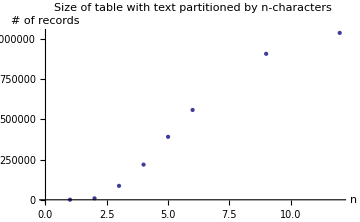

```mathematica
ListPlot[
{{1,Length[n1table]},{2,Length[n2table]},{3,Length[n3table]},{4,Length[n4table]},{5,Length[n5table]},{6,Length[n6table]},{9,Length[n9table]},{12,Length[n12table]}},
AxesLabel->{"n","# of records"},
PlotLabel->"Size of table with text partitioned by n-characters",
ImageSize->Medium
]
```

Why tweets? Their entropy is signficantly higher than standard English text.

```mathematica
Entropy[Characters[ExampleData[{"Text","OriginOfSpecies"}]]
]//N
```

2.97172

```mathematica
Entropy[
Characters[Flatten[payload]]
]//N
```

9.84093

How does the range of characters compare?

```mathematica
Length[DeleteDuplicates[Characters[ExampleData[{"Text","OriginOfSpecies"}]]]]
```

75

```mathematica
Length[DeleteDuplicates[Flatten[Characters[Flatten[payload]]]]]
```

787

That’s a lot of characters!

```mathematica
RandomSample[DeleteDuplicates[Flatten[Characters[Flatten[payload]]]],20]
```

{#,☻,ღ,ʕ,:dc89,!,t,k,,G,:dc47,:df66,:de11,:dde8,ｕ,:dc9b,à,ｉ,:de45,◇}

```mathematica
RandomSample[DeleteDuplicates[Flatten[Characters[Flatten[payload]]]],20]
```

{:dc61,:dc43,◠,,:de19,q,:dc46,:df35,:dc14,:de1d,:df80,r,:dc38,:dd5b,:dc89,:dca9,:dcd6,▆,:dc9e,Ｙ}

```mathematica
RandomSample[DeleteDuplicates[Flatten[Characters[Flatten[payload]]]],20]
```

{:de19,ط,,:ddeb,⭐,:df5d,:dc45,ك,:dc12,:dc52,ᴄ,:de3d,ة,,:dc93,:dc59,ᴅ,➄,:dc1f,6}

```mathematica
Length[Flatten[Characters[Flatten[payload]]]]
```

1515000

```mathematica
charcodes=Flatten[
ToCharacterCode[Flatten[Characters[Flatten[payload]]]]];
```

```mathematica
Min[charcodes]
```

10

```mathematica
Max[charcodes]
```

65533

The characters on the far left side of the graph are the standard English characters. The grouping around 10,000 are box drawing and dingbat characters. The grouping around 56,000 appear to be Korean characters.

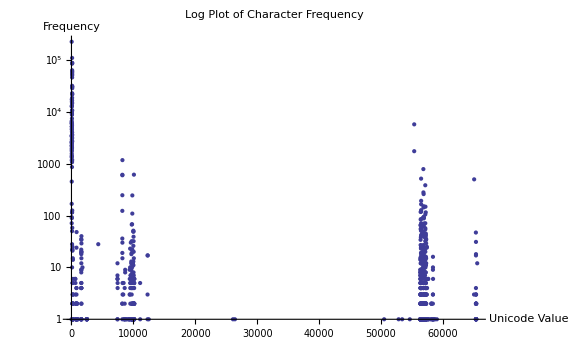

```mathematica
ListLogPlot[Tally[charcodes],
PlotLabel->"Log Plot of Character Frequency",
AxesLabel->{"Unicode Value","Frequency"},
ImageSize->Large
]
```

Given the higher entropy of tweets versus standard English, what is the branch count of the text? A branch, in this case, is an occurence of the last n-1 characters appearing as the first n-1 characters in a table entry. For example, with the entry {a,b,c,d,3}, and a table containing also {b,c,d,e,2}, {b,c,d,f,4}, and {c,d,f,g,5}, {a,b,c,d,3} has a branch count of 2, {b,c,d,f,4} has a branch count of 1, and {b,c,d,e,2} and {c,d,f,g,5} have branch counts of zero.

```mathematica
BranchCount[e_,list_]:=
Switch[Length[e]-1,
2,
Branch2Count[e,list],
3,
Branch3Count[e,list],
4,
Branch4Count[e,list],
5,
Branch5Count[e,list],
6,
Branch6Count[e,list],
9,
Branch9Count[e,list],
12,
Branch12Count[e,list]
]
```

```mathematica
Branch2Count[{_,e1_,_},list_]:=
Count[list,{e1,_,_}]
```

```mathematica
Branch3Count[{_,e1_,e2_,_},list_]:=
Count[list,{e1,e2,_,_}]
```

```mathematica
Branch4Count[{_,e1_,e2_,e3_,_},list_]:=
Count[list,{e1,e2,e3,_,_}]
```

```mathematica
Branch5Count[{_,e1_,e2_,e3_,e4_,_},list_]:=
Count[list,{e1,e2,e3,e4,_,_}]
```

```mathematica
Branch6Count[{_,e1_,e2_,e3_,e4_,e5_,_},list_]:=
Count[list,{e1,e2,e3,e4,e5,_,_}]
```

```mathematica
Branch9Count[{_,e1_,e2_,e3_,e4_,e5_,e6_,e7_,e8_,_},list_]:=
Count[list,{e1,e2,e3,e4,e5,e6,e7,e8,_,_}]
```

```mathematica
Branch12Count[{_,e1_,e2_,e3_,e4_,e5_,e6_,e7_,e8_,e9_,e10_,e11_,_},list_]:=
Count[list,{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,_,_}]
```

```mathematica
Branch4Count[{a,b,c,d,3},{{a,b,c,d,3},{b,c,d,e,2},{b,c,d,f,4},{c,d,f,g,5}}]
```

2

```mathematica
Branch4Count[{b,c,d,f,4},{{a,b,c,d,3},{b,c,d,e,2},{b,c,d,f,4},{c,d,f,g,5}}]
```

1

```mathematica
Branch4Count[{c,d,f,g,5},{{a,b,c,d,3},{b,c,d,e,2},{b,c,d,f,4},{c,d,f,g,5}}]
```

0

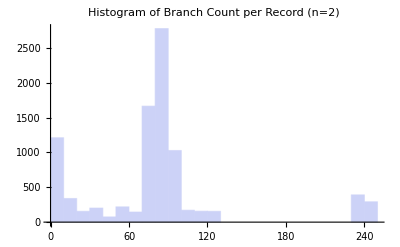

```mathematica
Histogram[
BranchCount[#,n2table]&/@n2table,
PlotLabel->"Histogram of Branch Count per Record (n=2)"
]
```

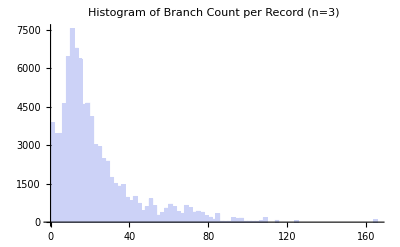

```mathematica
Histogram[
ParallelMap[BranchCount[#,n3table]&,n3table],
PlotLabel->"Histogram of Branch Count per Record (n=3)"
]
```

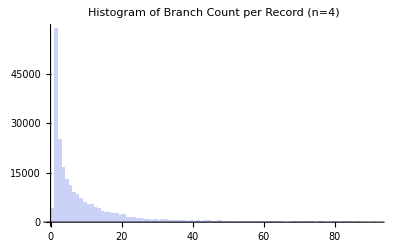

```mathematica
Histogram[
ParallelMap[BranchCount[#,n4table]&,n4table],
PlotLabel->"Histogram of Branch Count per Record (n=4)"
]
```

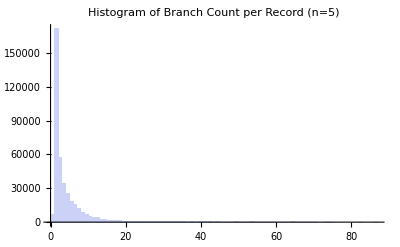

```mathematica
Histogram[
ParallelMap[BranchCount[#,n5table]&,n5table],
PlotLabel->"Histogram of Branch Count per Record (n=5)"
]
```

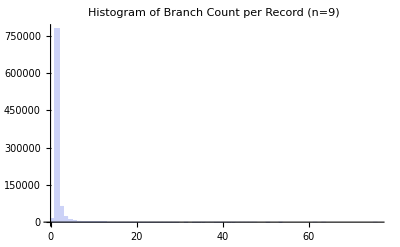

```mathematica
Histogram[
ParallelMap[BranchCount[#,n9table]&,n9table],
PlotLabel->"Histogram of Branch Count per Record (n=9)"
]
```

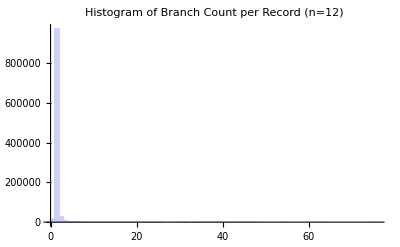

```mathematica
Histogram[
ParallelMap[BranchCount[#,n12table]&,n12table],
PlotLabel->"Histogram of Branch Count per Record (n=12)"
]
```

## Exporting

Recreating the tables is fairly expensive, so we will export the data for later use.

```mathematica
Export["Data/n2table.json",n2table]
```

Data/n2table.json

```mathematica
Export["Data/n3table.json",n3table]
```

Data/n3table.json

```mathematica
Export["Data/n4table.json",n4table]
```

Data/n4table.json

```mathematica
Export["Data/n5table.json",n5table]
```

Data/n5table.json

```mathematica
Export["Data/n6table.json",n6table]
```

Data/n6table.json

```mathematica
Export["Data/n9table.json",n9table]
```

Data/n9table.json

```mathematica
Export["Data/n12table.json",n12table]
```

Data/n12table.json